```mathematica
t0:=Function[{x,y},(x(x-1)+y^2)/(2(x+Sqrt[x]))]
worstT:=Function[{x,y},Piecewise[{
{t0[x,y],t0[x,y]>0},
{0,True}
}]]
```

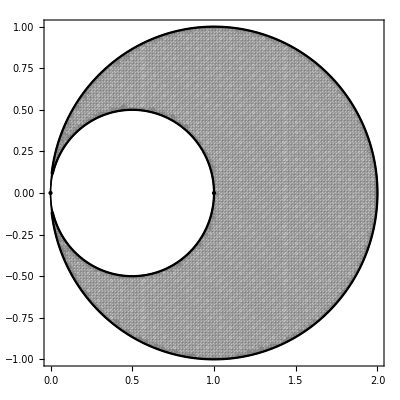

```mathematica
plot =Show[
RegionPlot[
{worstT[x,y]>0&&(x-1)^2+y^2<=1},
{x,0,2},
{y,-1,1},
PlotStyle->Directive[GrayLevel[0.5],Opacity[0.5]],(*Gray with 50% opacity*)
BoundaryStyle->Black (*Black border*),
PlotPoints->100
],
Graphics[{PointSize[Large],Point[{0,0}],Point[{1,0}]}]
]
```

```mathematica
Export[StringJoin[{NotebookDirectory[],"Ad_fail_at_0.png"},""],plot]
```

C:\Users\jared\Dropbox\Pony Express\Faulty Delivery\Mathematica\for_paper\Ad_fail_at_0.png